## 449 Homework #4

### 1-4) Townsend 11.1, 5, 6, 7.

11.1 E^1=(b(√(ℏ/mω)))^4⟨s^4⟩=(b(√(ℏ/mω)))^4⟨((a+a^†)/(√2))^4⟩.  Only terms with equal numbers of a&a^†survive:  Using a a^†=n+1,a^†a=n
E_n^1=(b(√(ℏ/mω)))^4 1/4⟨a a a^†a^†+a a^†a a^†+a a^†a^†a +a^†a^†a a+a^†a a^†a+a^†a a a^†⟩
=b/4(ℏ/(m ω))^2(√(n+1)(n+2)√(n+1) +(n+1)(n+1)+(n+1) n+√n(n-1)√n+n n+n (n+1))

```mathematica
b/4(ℏ/(m ω))^2(√(n+1)(n+2)√(n+1) +(n+1)(n+1)+(n+1) n+√n(n-1)√n+n n+n (n+1))//Simplify
```

(3 b (1+2 n+2 n^2) ℏ^2)/(4 m^2 ω^2)

b) At large n, E_n^1/E_n^0=b/4(ℏ/(m ω))^2 6 n^2/(ℏ ω n)∝n so perturbation theory doesn’t work at large n.

11.5

```mathematica
$Assumptions={A>0,μ𝔼>0};{eval,evec}=Eigensystem[{{μ𝔼, A}, {A, -μ𝔼}}];evec=Normalize/@evec//Simplify
```

{{(μ𝔼-√(A^2+μ𝔼^2))/(√2 √(A^2+μ𝔼 (μ𝔼-√(A^2+μ𝔼^2)))),1/(√(2+(2 μ𝔼 (μ𝔼-√(A^2+μ𝔼^2)))/A^2))},{(μ𝔼+√(A^2+μ𝔼^2))/(√2 √(A^2+μ𝔼 (μ𝔼+√(A^2+μ𝔼^2)))),1/(√(2+(2 μ𝔼 (μ𝔼+√(A^2+μ𝔼^2)))/A^2))}}

```mathematica
eval
```

{-√(A^2+μ𝔼^2),√(A^2+μ𝔼^2)}

```mathematica
evec0=evec/.μ𝔼->0//Simplify
```

{{-1/(√2),1/(√2)},{1/(√2),1/(√2)}}

perturbed + state

```mathematica
evec0⟦1⟧+evec0⟦2⟧  (evec0⟦2⟧ .{{μ𝔼, 0}, {0, -μ𝔼}}.evec0⟦1⟧)/(-2A)
```

{-1/(√2)+μ𝔼/(√2 A),1/(√2)+μ𝔼/(√2 A)}

perturbed - state

```mathematica
evec0⟦2⟧+evec0⟦1⟧  (evec0⟦1⟧ .{{μ𝔼, 0}, {0, -μ𝔼}}.evec0⟦2⟧)/(2A)
```

{1/(√2)+μ𝔼/(2 √2 A),1/(√2)-μ𝔼/(2 √2 A)}

```mathematica
Series[evec,{μ𝔼,0,1}]// Normal// PowerExpand
```

{{-1/(√2)+μ𝔼/(2 √2 A),1/(√2)+μ𝔼/(2 √2 A)},{1/(√2)+μ𝔼/(2 √2 A),1/(√2)-μ𝔼/(2 √2 A)}}

which agrees

11.6:  let ω_0=(-g q B_0)/(2 m c), ω_2=(-g q B_2)/(2 m c)

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

```mathematica
s=angmom[1/2];Eigensystem[Subscript[ω, 0] s⟦3⟧+Subscript[ω, 2] s⟦2⟧]
```

{{-1/2 √(ω_0^2+ω_2^2),1/2 √(ω_0^2+ω_2^2)},{{(ⅈ (-ω_0+√(ω_0^2+ω_2^2)))/ω_2,1},{-(ⅈ (ω_0+√(ω_0^2+ω_2^2)))/ω_2,1}}}

Taylor series

```mathematica
Series[%,{Subscript[ω, 2],0,2}]//Normal//PowerExpand
```

{{-ω_0/2-ω_2^2/(4 ω_0),ω_0/2+ω_2^2/(4 ω_0)},{{(ⅈ ω_2)/(2 ω_0),1},{-(2 ⅈ ω_0)/ω_2-(ⅈ ω_2)/(2 ω_0),1}}}

pert thy of spin up state

```mathematica
Subscript[ω, 0]/2+((q=Subscript[ω, 2]{0,1}.s⟦2⟧.{1,0})SuperStar[q])/Subscript[ω, 0]
```

ω_0/2+ω_2^2/(4 ω_0)

spin down

```mathematica
(-Subscript[ω, 0])/2+((q=Subscript[ω, 2]{0,1}.s⟦2⟧.{1,0})SuperStar[q])/(-Subscript[ω, 0])
```

-ω_0/2-ω_2^2/(4 ω_0)

agrees with Taylor series

11.7  Electric field inside nucleus ∝r, E=r/R e/R^2=-∂_r ((-e r^2)/(2 R^3)+const)→ Φ=(3e)/(2R)-(e r^2)/(2 R^3)→V=(-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)

V=Piecewise[{{-e^2/r, r>R}, {(-3 e^2)/(2R)+(e^2 r^2)/(2 R^3), r<R}}]=-e^2/r+Piecewise[{{0, r>R}, {(-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)+e^2/r, r<R}}]
E^1=⟨V_1⟩=∫d^3 r ψ^2(r)((-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)+e^2/r)≈ψ^2(0)∫d^3 r ((-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)+e^2/r)
(since the s-wave wavefunction is essentially constant over the volume of the proton)

```mathematica
ψ[0]^2 Integrate[4π((-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)+e^2/r)r^2,{r,0,R}]
```

2/5 e^2 π R^2 ψ[0]^2

```mathematica
%/.ψ[0]->Limit[ (Subscript[P, 1,0][s])/(s √(Subscript[a, B]^3))1/(√(4π)),s->0]
```

(2 e^2 R^2)/(5 a_B^3)

```mathematica
%/.{e^2->14.4 eV Å, R->1.2 10^-5 Å,Subscript[a, B]->0.5292 Å}
```

5.59662×10^-9 eV

or,

```mathematica
Integrate[((-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)+e^2/r/.r->Subscript[a, B] s)(2s )^2,{s,0,R/Subscript[a, B]}]//Simplify
```

(2 e^2 R^2)/(5 a_B^3)

the p-state wavefunction is extremely small inside the proton and will have even less effect.  The Ly-α radiation has slightly less energy due to the finite size of the proton.  This effect is readily observed with modern laser spectroscopy.

p-state: P_(2p)=(s^2 ⅇ^(-s/2))/(√24).   perturbation is isotropic so angular integration is 1  radial part is, taking the expontential in the radial function to be 1:

```mathematica
Integrate[((-3 e^2)/(2R)+(e^2 r^2)/(2 R^3)+e^2/r)(s^2/(√(24 Subscript[a, B])))^2/.s->r/Subscript[a, B],{r,0,R}]//Simplify
```

(e^2 R^4)/(1120 a_B^5)

```mathematica
%/.{e^2->14.4 eV Å, R->1.2 10^-5 Å,Subscript[a, B]->0.5292 Å}
```

6.42348×10^-21 eV

### 5) Calculate the g_j factors for a ^2 D_j state.

pick a j m_j state. Use CGs to calculate ⟨L_z+2 S_z⟩=⟨J_z⟩
j=5/2 m=5/2 5/2 5/2=2 1/2→⟨L_z+2 S_z⟩=3=g_j⟨J_z⟩=g_j 5/2→ g_(5/2)=6/5 
j=3/2 m=3/2 3/2 3/2=2/(√5)2 -1/2-1/(√5)1 1/2→⟨L_z+2 S_z⟩= 4/5(1)+1/5(2)=6/5=g_j⟨J_z⟩=g_j 3/2→ g_(3/2)=4/5 
where I used

```mathematica
{ClebschGordan[{2,2},{1/2,-1/2},{3/2,3/2}],ClebschGordan[{2,1},{1/2,1/2},{3/2,3/2}]}
```

{2/(√5),-1/(√5)}

### 6) The 97d^2 D_j states of Rb have a fine-structure splitting of h×12.2 MHz. Calculate the energy levels as a function of magnetic field, and make a plot showing both the exact results and the approximate answers from 5).

exact calc

```mathematica
s=angmom[1/2];l=angmom[2];Hso=2/5 Sum[l⟦p⟧⊗s⟦p⟧,{p,3}];Eigenvalues[Hso]
```

{-3/5,-3/5,-3/5,-3/5,2/5,2/5,2/5,2/5,2/5,2/5}

Let a=(μ B)/E_so=B/(8.72 Gauss)

```mathematica
(12.2 MHz)/(1.3996 MHz/Gauss)
```

8.71678 Gauss

```mathematica
eD=Eigenvalues[ H=Hso+a (2 IdentityMatrix[5]⊗s⟦3⟧+l⟦3⟧⊗IdentityMatrix[2])]
```

{1/5 (2-15 a),1/5 (2+15 a),1/10 (-1-15 a-√5 √(5-6 a+5 a^2)),1/10 (-1-15 a+√5 √(5-6 a+5 a^2)),1/10 (-1-5 a-√5 √(5-2 a+5 a^2)),1/10 (-1-5 a+√5 √(5-2 a+5 a^2)),1/10 (-1+5 a-√5 √(5+2 a+5 a^2)),1/10 (-1+5 a+√5 √(5+2 a+5 a^2)),1/10 (-1+15 a-√5 √(5+6 a+5 a^2)),1/10 (-1+15 a+√5 √(5+6 a+5 a^2))}

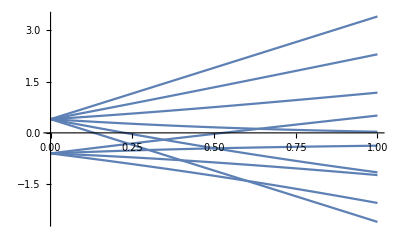

```mathematica
exact=Plot[Sort[eD],{a,0,1}]
```

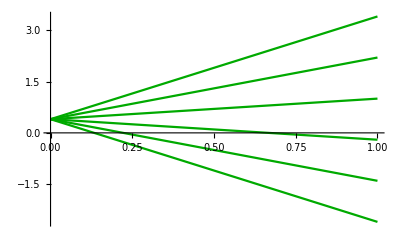

```mathematica
D52=Plot[Sort[2/5+a 6/5 Range[-5/2,5/2]],{a,0,1},PlotStyle->Darker[Green]]
```

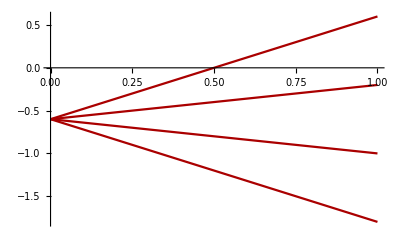

```mathematica
D32=Plot[Sort[-3/5+a 4/5 Range[-3/2,3/2]],{a,0,1},PlotStyle->Darker[Red]]
```

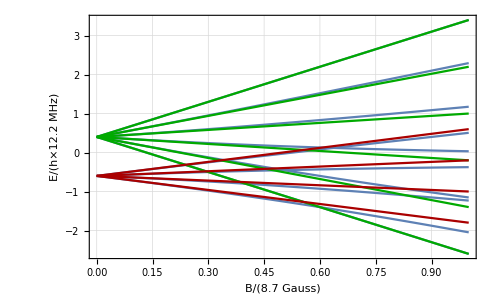

```mathematica
ThadPlot[Show[exact,D52,D32],{"B/(8.7 Gauss)","E/(h×12.2 MHz)"}]
```